```mathematica
Directory[]
```

C:\Users\anhkh\Documents

```mathematica
eps=8.854 10^-12;
clb=1.602 10^-19;
(k=1/(4Pi eps))//N
```

8.98774×10^9

```mathematica
k (100 100)/((10^-9)^2)clb^2
```

2.30662×10^-6

```mathematica
k (100 100)/((10^-9)^2)
```

8.98774×10^31

## Varying q1 and q2

```mathematica
q2=100;
r=10^-9;
```

```mathematica
q1=Table[RandomVariate[NormalDistribution[100 +50 u,σq=10],1],{u,0,9}]//Flatten
f=Table[RandomVariate[NormalDistribution[q1[[u]] clb^2/r^2 q2 k,σf=1 10^-6],1],{u,1,10}]//Transpose//Flatten
```

{99.1673,156.208,199.62,256.641,309.525,352.376,389.25,455.65,507.717,555.733}

{8.64564×10^-7,2.85096×10^-6,3.30593×10^-6,4.79083×10^-6,7.53492×10^-6,6.77385×10^-6,9.40037×10^-6,8.73404×10^-6,0.0000126394,0.0000112597}

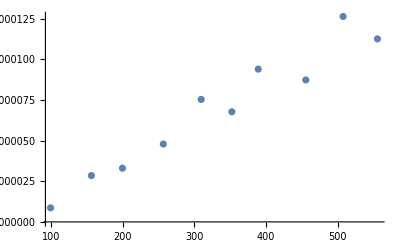

```mathematica
ListPlot[Thread[{q1,f}]]
```

```mathematica
Export["varying-q1.txt",Thread[{q1,σq,f,σf}]//N,"CSV"]
```

varying-q1.txt

```mathematica
q1=Table[RandomVariate[NormalDistribution[100 +50 u,10],1],{u,0,9}]//Flatten;
f=Table[RandomVariate[NormalDistribution[q1[[u]] clb^2/r^2 q2 k,σf=1 10^-6],1],{u,1,10}]//Transpose//Flatten;
Export["varying-q2.txt",Thread[{q1,σq,f,σf}//N],"CSV"]
```

varying-q2.txt

## Varying θ

```mathematica
q1=400;
q2=400;
r=10^-9;
```

{-0.167376,4.67212,9.09136,13.0863,19.2297,25.6107,32.0563,36.0867,38.1836,42.4873}

{0.00003701,0.0000365142,0.0000368823,0.0000369411,0.0000364852,0.0000382241,0.0000362747,0.0000369122,0.0000377385,0.0000369601}

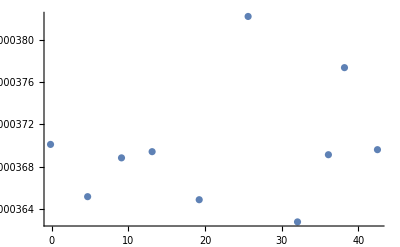

varying-theta.txt

```mathematica
θ=Table[RandomVariate[NormalDistribution[0+5u,σθ=2],1],{u,0,9}]//Flatten
f=Table[RandomVariate[NormalDistribution[q1 clb^2/r^2 q2 k,σf=0.5 10^-6],1],{u,1,10}]//Transpose//Flatten
ListPlot[Thread[{θ,f}]]
Export["varying-theta.txt",Thread[{θ,σθ,f,σf}],"CSV"]
```

## Varying r

```mathematica
q1=400;
q2=400;
r=Table[0,{u,1,3}];
f=Table[0,{u,1,3}];
```

```mathematica
r[[1]]=Table[RandomVariate[NormalDistribution[10^-9+0.1u 10^-9,0.2 10^-9],1],{u,0,4}]//Flatten
f[[1]]=Table[RandomVariate[NormalDistribution[q1 clb^2/(r[[1]][[u]])^2 q2 k,0.1 10^-6],1],{u,1,5}]//Transpose//Flatten
ListPlot[Thread[{r[[1]],f[[1]]}]]
```

```mathematica
r[[1]]={1.2362298956574304*^-9,1.046680822741696*^-9,9.430048510423208*^-10,1.2454241924894795*^-9,1.1264197710539184*^-9};
f[[1]]={0.000024168359500366657,0.00003377888714794865,0.000041495802506341804,0.00002361354501949803,0.000028959299148118893};
{σr,σf}={0.2 10^-9,0.1 10^-6};
```

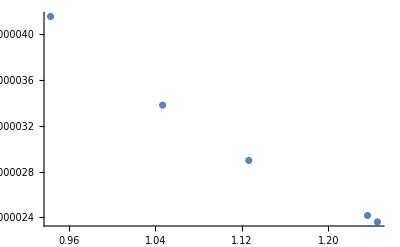

```mathematica
ListPlot[Thread[{r[[1]],f[[1]]}]]
```

```mathematica
Export["varying-r1.txt",Thread[{r[[1]],σr,f[[1]],σf}],"CSV"]
```

varying-r1.txt

```mathematica
σf=Table[0,{u,1,10}];
```

{2.23186×10^-7,1.43214×10^-7,1.2328×10^-7,2.06136×10^-7,1.79226×10^-7,2.84362×10^-7,2.33763×10^-7,2.90895×10^-7,2.89099×10^-7,1.82339×10^-7}

{7.43399×10^-10,1.83382×10^-9,2.3667×10^-9,8.77639×10^-10,1.2182×10^-9,4.48662×10^-10,6.98103×10^-10,4.91754×10^-10,4.34723×10^-10,1.2376×10^-9}

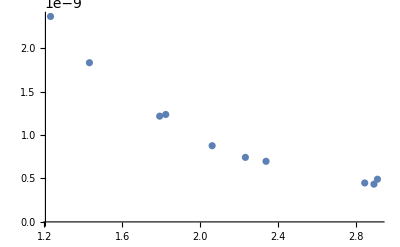

```mathematica
r[[2]]=Table[RandomVariate[NormalDistribution[10^-7+0.2u 10^-7,σr=0.5 10^-7],1],{u,0,9}]//Flatten
f[[2]]=Table[RandomVariate[NormalDistribution[q1 clb^2/(r[[2]][[u]])^2 q2 k,σf[[u]]=0.05 q1 clb^2/(r[[2]][[u]])^2 q2 k],1],{u,1,10}]//Transpose//Flatten
ListPlot[Thread[{r[[2]],f[[2]]}]]
```

```mathematica
σf
```

{3.70452×10^-11,8.997×10^-11,1.21418×10^-10,4.34266×10^-11,5.74467×10^-11,2.28203×10^-11,3.37687×10^-11,2.18068×10^-11,2.20786×10^-11,5.55015×10^-11}

```mathematica
Export["varying-r2.txt",Thread[{r[[2]],σr,f[[2]],σf}],"CSV"]
```

varying-r2.txt

```mathematica
σf=Table[0,{u,1,10}];
```

{1.00811×10^-9,5.00683×10^-8,1.00692×10^-7,1.51274×10^-7,2.01994×10^-7,2.50436×10^-7,3.01885×10^-7,3.50974×10^-7,4.00923×10^-7,4.5057×10^-7}

{0.0000344698,1.54282×10^-8,3.83749×10^-9,1.71398×10^-9,9.05852×10^-10,5.74624×10^-10,3.95926×10^-10,2.66494×10^-10,2.18874×10^-10,1.76168×10^-10}

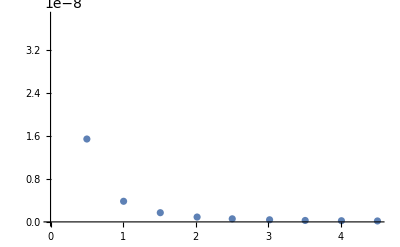

```mathematica
r[[3]]=Table[RandomVariate[NormalDistribution[10^-9+50u 10^-9,σr=0.5 10^-9],1],{u,0,9}]//Flatten
f[[3]]=Table[RandomVariate[NormalDistribution[q1 clb^2/(r[[3]][[u]])^2 q2 k,σf[[u]]=0.1 q1 clb^2/(r[[3]][[u]])^2 q2 k],1],{u,1,10}]//Transpose//Flatten
ListPlot[Thread[{r[[3]],f[[3]]}]]
```

```mathematica
Export["varying-r3.txt",Thread[{r[[3]],σr,f[[3]],σf}],"CSV"]
```

varying-r3.txt